Set up the function to be experimented with. It should have a somewhat slowly converging Fourier series because its first derivative is not smooth at the boundary of the periodic cell.

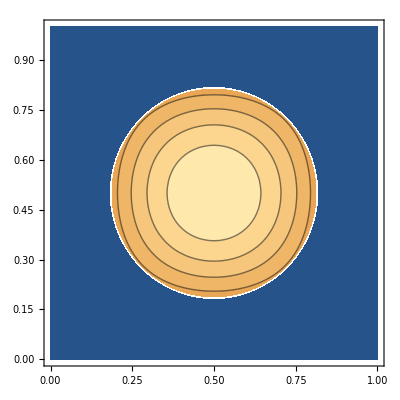

```mathematica
(*f1[x_,y_]:=Piecewise[{{Sin[π x]Sin[π y],(x>1/4 &&x<3/4)&&(y>1/4 &&y<3/4)}}]*)
f1[x_,y_]:=Piecewise[{{Sin[π x]Sin[π y],(x-1/2)^2+(y-1/2)^2<1/10}}]
GraphicsRow[{Plot3D[f1[x,y],{x,0,1},{y,0,1}],ContourPlot[f1[x,y],{x,0,1},{y,0,1}]}]
```

```mathematica
analAns=NIntegrate[f1[x,y],{x,0,1},{y,0,1}]//Chop
```

0.242763

```mathematica
npts = 40;
xpts = Subdivide[npts]⟦;;-2⟧;(* Don't include last point *)
ypts = xpts;
samples =Table[f1[x,y],{x,xpts},{y,ypts}];
numAns =Plus@@(samples//Flatten)/npts^2;
analAns-numAns//N
```

0.00198648

```mathematica
sqNumInt[n_]:=Module[{xpts,ypts},
xpts = Subdivide[n]⟦;;-2⟧;(* Don't include last point *)
ypts = xpts;
samples =Table[f1[x,y],{x,xpts},{y,ypts}];
numAns =Plus@@(samples//Flatten)/n^2;
{n^2,analAns-numAns//N}]
```

```mathematica
sqNumInt[10]
```

{100,0.0149345}

```mathematica
sqDat =Table[sqNumInt[10 2^n],{n,1,6}]
```

{{400,0.00689051},{1600,0.00198648},{6400,0.000150213},{25600,0.000119947},{102400,6.77186×10^-6},{409600,3.67317×10^-6}}

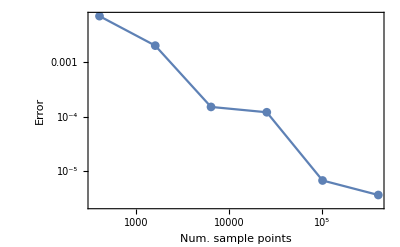

/Users/hart/papers.git/opf_kgrids/figs/convergence.pdf

```mathematica
sqPlot=ListLogLogPlot[sqDat,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Num. sample points","Error"},GridLines->Automatic]
Export["/Users/hart/papers.git/opf_kgrids/figs/convergence.pdf",%]
```

```mathematica
hexNumInt[n_]:=Module[{xpts,ypts,h,w},
xpts = Subdivide[4n]⟦;;-2⟧;(* Don't include last point *)
ypts = Subdivide[7 n]⟦;;-2⟧;(* Don't include last point *)
w=xpts⟦2⟧;h=ypts⟦2⟧;
samples =Table[{f1[x+w/2,y],f1[x+w/4,y+h/2],f1[x+3/4w,y+h/2],f1[x,y]},{x,xpts},{y,ypts}];
numAns =Plus@@(samples//Flatten)/(4 4 7 n^2);
{4 4 7 n^2,analAns-numAns//N}]
```

```mathematica
hexDat=Table[hexNumInt[2^n],{n,1,5}]
```

{{448,0.0217314},{1792,0.0104626},{7168,0.00528132},{28672,0.0026527},{114688,0.0013293}}

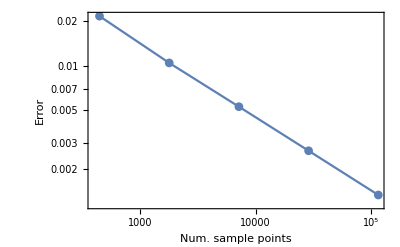

```mathematica
hexPlot= ListLogLogPlot[hexDat,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Num. sample points","Error"},BaseStyle->{FontSize->18}]
```

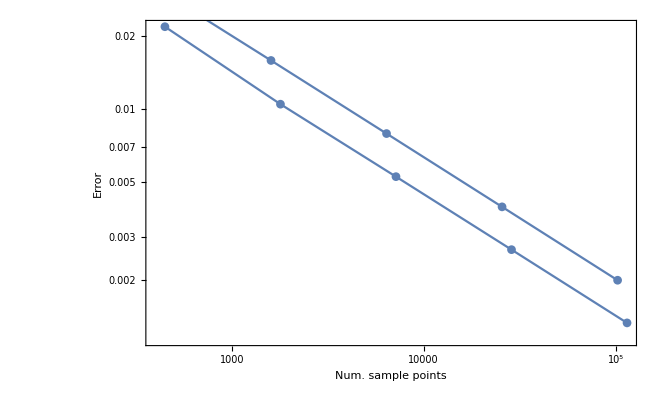

```mathematica
Show[{hexPlot,sqPlot}]
```

3D old example. Maybe periodic cases (smooth) the savings isn’t as large as cases where the FT is slowly converging...

```mathematica
10^3/13^3//N
```

0.455166

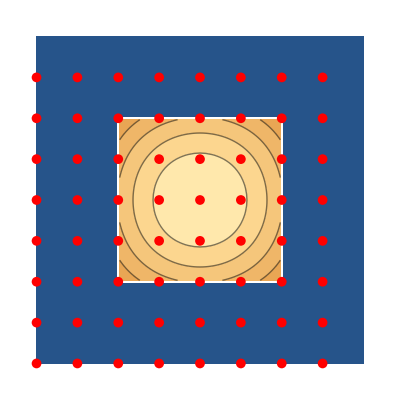

```mathematica
squarepic=Show[{ContourPlot[f1[x,y],{x,0,1},{y,0,1},Frame->None],ListPlot[Table[{x,y},{x,Subdivide[8]⟦;;-2⟧},{y,Subdivide[8]⟦;;-2⟧}]//Flatten[#,1]&,PlotStyle->Red,PlotMarkers->{Automatic,10}]}]
(* Export["/Users/hart/papers.git/opf_kgrids/figs/mp_example.png",%]*)
```

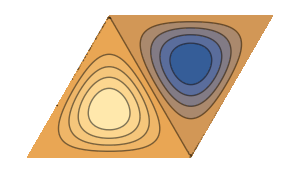

```mathematica
rhomb=ContourPlot[Sin[n π y]Sin[m π (√(3/4)x+1/2 y)]Sin[l π (√(3/4)x-1/2 y)]/.{n->1,m->1,l->1},{x,0,Sqrt[3]},{y,0,1},ImageSize->300,Contours->14,PlotRange->{-1,1},AspectRatio->1/Sqrt[3],RegionFunction->Function[{x,y},x-y /Sqrt[3]>0&&x-y /Sqrt[3]<2/Sqrt[3]],Frame->None]
```

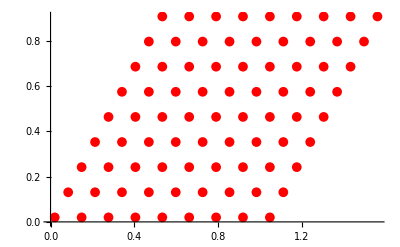

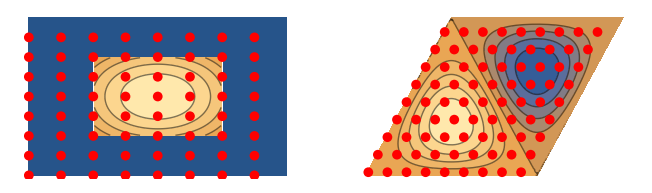

/Users/hart/papers.git/opf_kgrids/figs/mp_example.png

```mathematica
rhombpts=ListPlot[Table[{x +y/Sqrt[3]+.02, y+.02},{x,Subdivide[9]⟦;;-2⟧2/Sqrt[3]},{y,Subdivide[9]⟦;;-2⟧}]//Flatten[#,1]&,PlotStyle->Red,PlotMarkers->{Automatic,10}]
MPpic=GraphicsGrid[{{squarepic,Show[rhomb,rhombpts]}}]
Export["/Users/hart/papers.git/opf_kgrids/figs/mp_example.png",MPpic]
```

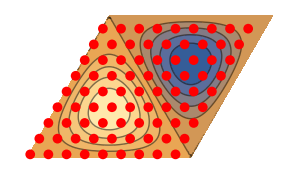

```mathematica
Show[rhomb,rhombpts]
```

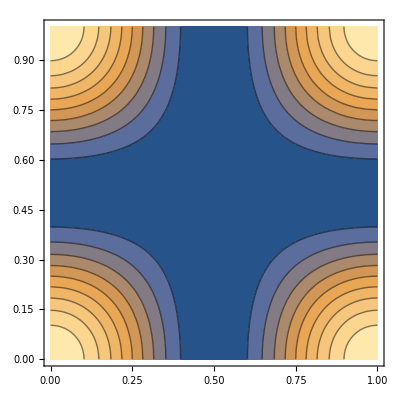

```mathematica
f2[x_,y_]:=Exp[Cos[2π x]+Cos[2π y]]
f2[x_,y_]:=Cos[π x]^2 Cos[π y]^2
GraphicsRow[{Plot3D[f2[x,y],{x,0,1},{y,0,1}],ContourPlot[f2[x,y],{x,0,1},{y,0,1}]}]
```

```mathematica
analAns2=Integrate[f2[x,y],{x,0,1},{y,0,1}]
```

1/4

```mathematica
sqNumInt2[n_]:=Module[{xpts,ypts,numAns2,samples},
xpts = Subdivide[n]⟦;;-2⟧;(* Don't include last point *)
ypts = xpts;
samples =Table[f2[x,y],{x,xpts},{y,ypts}];
numAns2 =Plus@@(samples//Flatten)/n^2;
{n^2,analAns2-numAns2//N}]
```

```mathematica
sqNumInt2[4]
```

{16,0.}

```mathematica
sqDat2 =Table[sqNumInt2[2^n],{n,1,5}]
```

{{4,0.},{16,0.},{64,0.},{256,0.},{1024,0.}}

```mathematica
hexNumInt2[n_]:=Module[{xpts,ypts,h,w,samples,numAns2},
xpts = Subdivide[4n]⟦;;-2⟧;(* Don't include last point *)
ypts = Subdivide[7 n]⟦;;-2⟧;(* Don't include last point *)
w=xpts⟦2⟧;h=ypts⟦2⟧;
samples =Table[{f2[x+w/2,y],f2[x+w/4,y+h/2],f2[x+3/4w,y+h/2],f2[x,y]},{x,xpts},{y,ypts}];
numAns2 =Plus@@(samples//Flatten)/(4 4 7 n^2);
{4 4 7 n^2,analAns2-numAns2//N}]
```

```mathematica
hexDat2=Table[hexNumInt2[n],{n,1,5}]
```

{{112,0.},{448,0.},{1008,5.55112×10^-17},{1792,0.},{2800,0.}}

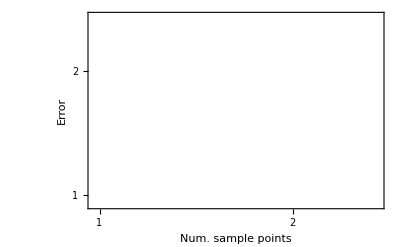

```mathematica
sqPlot2=ListLogLogPlot[Abs[sqDat2],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Num. sample points","Error"},GridLines->Automatic];
hexPlot2= ListLogLogPlot[Abs[hexDat2],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Num. sample points","Error"},BaseStyle->{FontSize->18}];
Show[sqPlot2,hexPlot2]
```

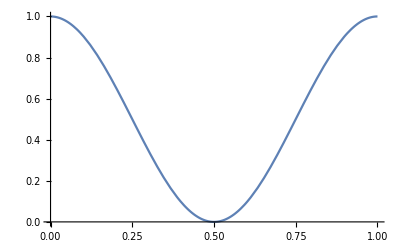

1/2

```mathematica
Plot[Cos[π x]^2,{x,0,1}]
Integrate[Cos[π x]^2,{x,0,1}]
```

```mathematica
FourierSeries[Cos[π x]^2,x,3]
```

1/2 (1+(Cos[π^2] Sin[π^2])/π^2)+(ⅇ^(-2 ⅈ x) Sin[2 π^2])/(4 (-1+π^2))+(ⅇ^(2 ⅈ x) Sin[2 π^2])/(4 (-1+π^2))-(ⅇ^(-3 ⅈ x) Sin[2 π^2])/(-9+4 π^2)-(ⅇ^(3 ⅈ x) Sin[2 π^2])/(-9+4 π^2)-(ⅇ^(-ⅈ x) Sin[2 π^2])/(-1+4 π^2)-(ⅇ^(ⅈ x) Sin[2 π^2])/(-1+4 π^2)

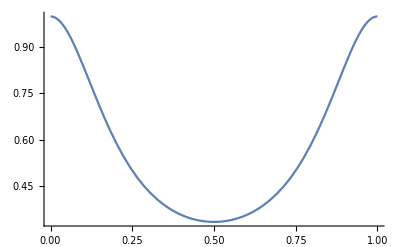

1/(√3)

```mathematica
Plot[1/(2-Cos[2π x]),{x,0,1}]
Integrate[1/(2-Cos[2π x]),{x,0,1}]
```

```mathematica
Integrate[Sin[π x]Sin[π y],{x,1/4,3/4},{y,1/4,3/4}]
```

2/π^2